```mathematica
Map[Factor,f[{x,y}]]
xsub=Solve[f[{x,y}]⟦2⟧==0,x]
{f[{2y,y}],Simplify[f[{2y,y}]]
CPs = Round[CPs];
As=Map[df,CPs];
Map[MatrixForm,As]
CharPolys=Map[CharacteristicPolynomial[#,λ]&,As]
Map[Factor,CharPolys]
Map[λ/.Solve[#==0,λ]&,CharPolys]
```

{2 (-4-2 y+x y),-((x-2 y) (x+2 y))}

{{x→-2 y},{x→2 y}}

```mathematica
f[{x,y}]
```

{-8+(-4+2 x) y,(-x+2 y) (x+2 y)}

```mathematica
df[{x_,y_}]=D[f[{x,y}],{{x,y}}];
cp={-2,-1};
A=df[cp];
MatrixForm[A]
Eigenvalues[A]
CharacteristicPolynomial[A,λ]
```

(-2 | -8
4 | -8)

{-5+ⅈ √23,-5-ⅈ √23}

48+10 λ+λ^2

```mathematica
4
```

{{2 y,-4+2 x},{-2 x,2 (-x+2 y)+2 (x+2 y)}}

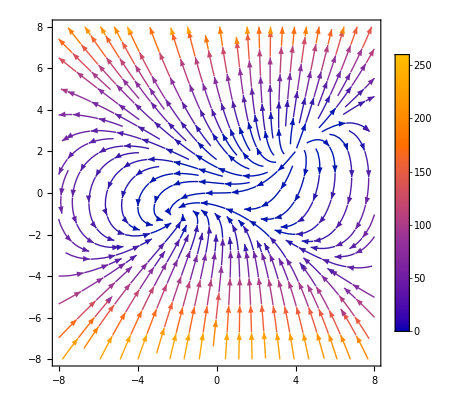

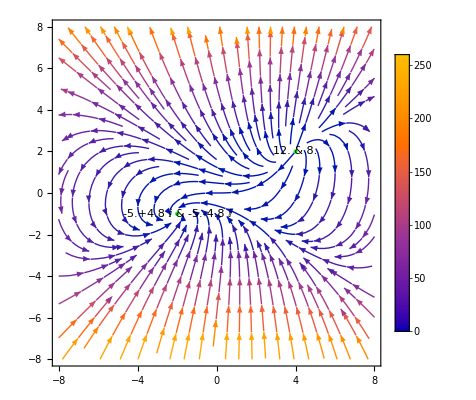

```mathematica
Clear[f,df,x,y]
f[{x_,y_}]:={(2x-4)y-8, (2y-x)(2y+x)}
df[{x_,y_}]=D[f[{x,y}],{{x,y}}]
CPs=NSolveValues[f[{x,y}]=={0,0},{x,y},Reals];
λs=Map[ Eigenvalues[df[#]]&,CPs];
StreamPic=StreamPlot[ f[{x,y}],{x,-8,8},{y,-8,8},
PlotLegends->Automatic
]
Show[StreamPic,
Epilog->Table[ 
{λ1,λ2}=λs⟦i⟧;
{
Text[
StringForm["`` & ``",NumberForm[λ1,2],NumberForm[λ2,2]],CPs⟦i⟧,{0,-1.2},Background->LightGreen],
Green,Point[CPs⟦i⟧]
},{i,Length[CPs]}]]
```

```mathematica
LinPic=Show[
Table[
{xCP,yCP}=CPs⟦i⟧;
A=df[{xCP,yCP}];
StreamPlot[A.{x-xCP,y-yCP},{x,xCP-1,xCP+1},{y,yCP-1,yCP+1},
StreamPoints->10,StreamScale->Tiny,RegionFillingStyle->None,RegionBoundaryStyle->Red,
RegionFunction->Function[{x,y},Norm[{x-xCP,y-yCP}]<1]],
{i,1,Length[CPs]}],
PlotRange->{{-8,8},{-8,8}},
AspectRatio->Automatic
];
TabView[{
"Linearizations"->LinPic,
"Match"->Show[StreamPic,LinPic]
}]
```

12

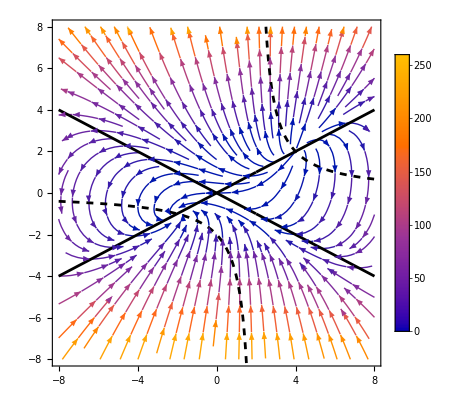

```mathematica
Show[StreamPic,Plot[{x/2,-x/2, 8/(2x-4)},{x,-8,8},PlotStyle->{Black,Black,Directive[Black,Dashed]}],
PlotRange->{{-8,8},{-8,8}}]
```